# Hilbert Curve

### Author

Eric W. Weisstein
January 6, 2011

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Fractals/HilbertCurve.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/HilbertCurve.html.

For a list of Eric's math packages that may be needed to evaluate this notebook, see Mathematica Information Center's MathSource item 4775.  A list of Eric's utility packages that may be needed to evaluate this notebook may be downloaded from MathSource item 5087.

©2010 Wolfram Research, Inc. except for portions noted otherwise

### Additional Authors

3-D Hilbert curve by
Michael Trott
The Mathematica GuideBook for Programming.
New York: Springer-Verlag, p. 97, 2004

### Initialization

```mathematica
<<MathWorld`Fractal`
```

## Plots

### Hilbert I

```mathematica
CurveArray[Hilbert,{1,5},2000,ImageSize->500]
```

⁃GraphicsArray⁃

### Hilbert II

```mathematica
CurveArray[HilbertII,{1,3},10^4,ImageSize->500]
```

⁃GraphicsArray⁃

### Both

#### V6

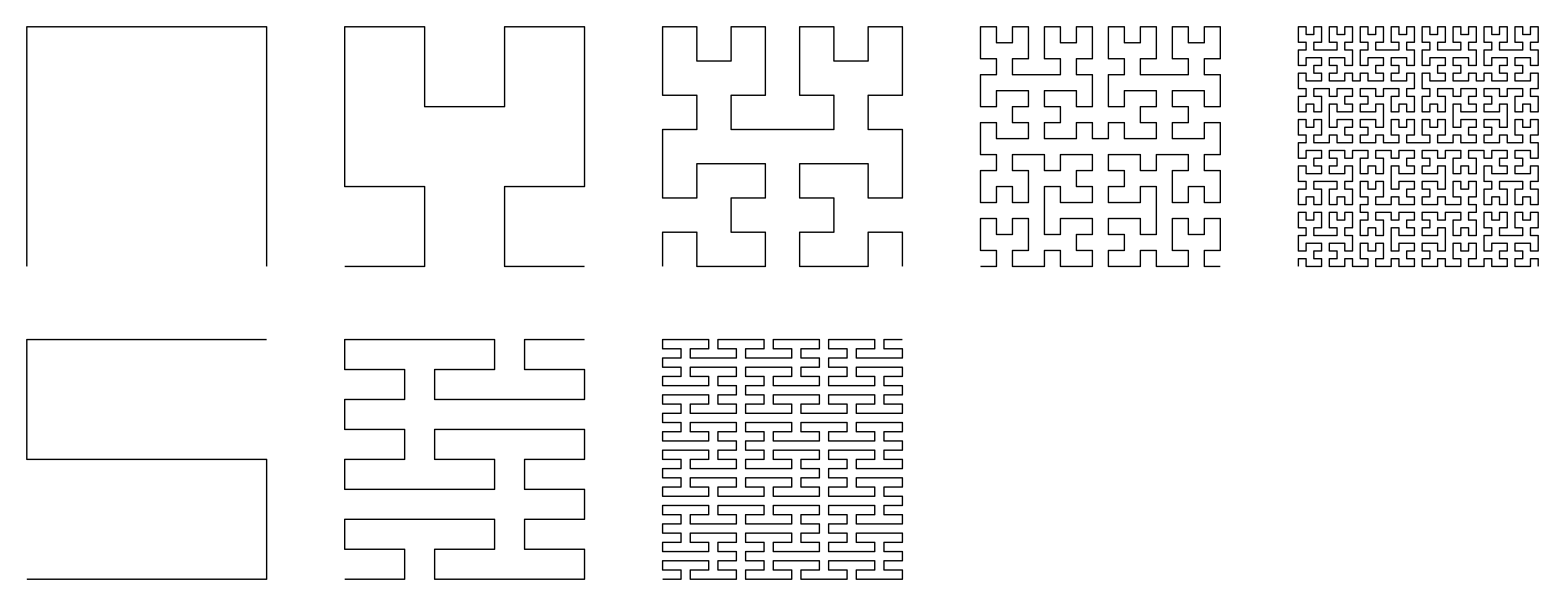

```mathematica
GraphicsGrid[{Hilbert[#,2000]&/@Range[5],HilbertII[#,10^4]&/@Range[3]}]
```

## 3-D